## Input

```mathematica
mh:=√2;
dmh:=0.01;
mw:=1/(√2);
n:=20;

x0=10.0;
y0=0.01;
z0=0.008;

xf=1;
yf=1;
zf=1;
```

An initial value for the derivative dy/dx  is assumed and will be adjusted to satisfy the second boundary condition.

```mathematica
dydx1=-0.1;
dzdx1=-0.2;
```

An second value for the derivative dy/dx is assumed here as well to be used in second iteration.

```mathematica
dydx2=-0.5;
dzdx2=-1.0;
```

## Setup

x is rho.

dF/dx = q,   dq/dx = 2 mh q - mh / 4x * z^2,  dG/dx = w,  dw/dx = mh w + 2z/x^2 - mh/4x * exp(-mh x) * y* z

```mathematica
f1[x_,y_,z_,q_,w_]:=q;
```

```mathematica
f2[x_,y_,z_,q_,w_]:=2*mh*q-(mh*z^2)/(4*x);
```

```mathematica
f3[x_,y_,z_,q_,w_]:=w;
```

```mathematica
f4[x_,y_,z_,q_,w_]:=mh*w+(2*z)/x^2-mh/(4*x)*ⅇ^(-mh*x)*y*z;
```

Includes the fact that we go to the left

```mathematica
h=(xf-x0)/n
```

-0.45

## First Iteration

```mathematica
X1[0]=x0
Y1[0]=y0
Z1[0]=z0
Q1[0]=dydx1
W1[0]=dzdx1

For[i=0,i<n,i++,
X1[i+1]=X1[i]+h;

k1y=f1[X1[i],Y1[i],Z1[i],Q1[i],W1[i]];
k1z=f2[X1[i],Y1[i],Z1[i],Q1[i],W1[i]];
k1q=f3[X1[i],Y1[i],Z1[i],Q1[i],W1[i]];
k1w=f4[X1[i],Y1[i],Z1[i],Q1[i],W1[i]];

k2y=f1[X1[i]+0.5*h,Y1[i]+0.5*k1y*h,Z1[i]+0.5*k1z*h,Q1[i]+0.5*k1q*h,W1[i]+0.5*k1w*h];
k2z=f2[X1[i]+0.5*h,Y1[i]+0.5*k1y*h,Z1[i]+0.5*k1z*h,Q1[i]+0.5*k1q*h,W1[i]+0.5*k1w*h];
k2q=f3[X1[i]+0.5*h,Y1[i]+0.5*k1y*h,Z1[i]+0.5*k1z*h,Q1[i]+0.5*k1q*h,W1[i]+0.5*k1w*h];
k2w=f4[X1[i]+0.5*h,Y1[i]+0.5*k1y*h,Z1[i]+0.5*k1z*h,Q1[i]+0.5*k1q*h,W1[i]+0.5*k1w*h];

k3y=f1[X1[i]+0.5*h,Y1[i]+0.5*k2y*h,Z1[i]+0.5*k2z*h,Q1[i]+0.5*k2q*h,W1[i]+0.5*k2w*h];
k3z=f2[X1[i]+0.5*h,Y1[i]+0.5*k2y*h,Z1[i]+0.5*k2z*h,Q1[i]+0.5*k2q*h,W1[i]+0.5*k2w*h];
k3q=f3[X1[i]+0.5*h,Y1[i]+0.5*k2y*h,Z1[i]+0.5*k2z*h,Q1[i]+0.5*k2q*h,W1[i]+0.5*k2w*h];
k3w=f4[X1[i]+0.5*h,Y1[i]+0.5*k2y*h,Z1[i]+0.5*k2z*h,Q1[i]+0.5*k2q*h,W1[i]+0.5*k2w*h];

k4y=f1[X1[i]+h,Y1[i]+k3y*h,Z1[i]+k3z*h,Q1[i]+k3q*h,W1[i]+k3w*h];
k4z=f2[X1[i]+h,Y1[i]+k3y*h,Z1[i]+k3z*h,Q1[i]+k3q*h,W1[i]+k3w*h];
k4q=f3[X1[i]+h,Y1[i]+k3y*h,Z1[i]+k3z*h,Q1[i]+k3q*h,W1[i]+k3w*h];
k4w=f4[X1[i]+h,Y1[i]+k3y*h,Z1[i]+k3z*h,Q1[i]+k3q*h,W1[i]+k3w*h];

Y1[i+1]=Y1[i]+1/6*(k1y+2*k2y+2*k3y+k4y)*h;
Z1[i+1]=Z1[i]+1/6*(k1z+2*k2z+2*k3z+k4z)*h;
Q1[i+1]=Q1[i]+1/6*(k1q+2*k2q+2*k3q+k4q)*h;
W1[i+1]=W1[i]+1/6*(k1w+2*k2w+2*k3w+k4w)*h;
]
```

10.

0.01

0.008

-0.1

-0.2

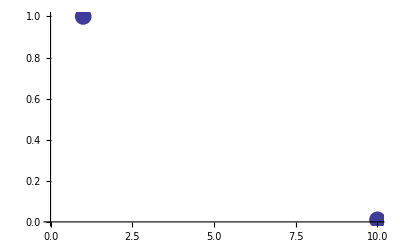

```mathematica
plot1=ListPlot[{{x0,y0},{xf,yf}},PlotStyle->PointSize[0.03],AxesOrigin->{0,0}]
```

```mathematica
data1=Table[{X1[i],Y1[i]},{i,0,20}];
data2=Table[{X1[i],Z1[i]},{i,0,20}];
plot2=ListPlot[data1,Joined->True,PlotStyle->{Thickness[0.002],RGBColor[0,1,0]},DisplayFunction->Identity];
plot3=ListPlot[data2,Joined->True,PlotStyle->{Thickness[0.002],RGBColor[1,1,0]},DisplayFunction->Identity];
```

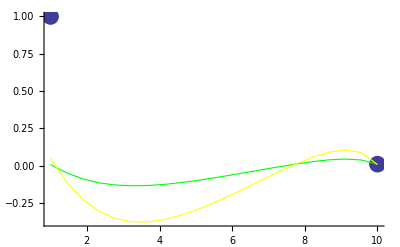

```mathematica
Show[plot1,plot2,plot3,Axes->True,AxesOrigin->{0,0},PlotRange->Automatic]
```

## Second Iteration

```mathematica
X2[0]=x0
Y2[0]=y0
Z2[0]=z0
Q2[0]=dydx2
W2[0]=dzdx2

For[i=0,i<n,i++,
X2[i+1]=X2[i]+h;

k1y=f1[X2[i],Y2[i],Z2[i],Q2[i],W2[i]];
k1z=f2[X2[i],Y2[i],Z2[i],Q2[i],W2[i]];
k1q=f3[X2[i],Y2[i],Z2[i],Q2[i],W2[i]];
k1w=f4[X2[i],Y2[i],Z2[i],Q2[i],W2[i]];

k2y=f1[X2[i]+0.5*h,Y2[i]+0.5*k1y*h,Z2[i]+0.5*k1z*h,Q2[i]+0.5*k1q*h,W2[i]+0.5*k1w*h];
k2z=f2[X2[i]+0.5*h,Y2[i]+0.5*k1y*h,Z2[i]+0.5*k1z*h,Q2[i]+0.5*k1q*h,W2[i]+0.5*k1w*h];
k2q=f3[X2[i]+0.5*h,Y2[i]+0.5*k1y*h,Z2[i]+0.5*k1z*h,Q2[i]+0.5*k1q*h,W2[i]+0.5*k1w*h];
k2w=f4[X2[i]+0.5*h,Y2[i]+0.5*k1y*h,Z2[i]+0.5*k1z*h,Q2[i]+0.5*k1q*h,W2[i]+0.5*k1w*h];

k3y=f1[X2[i]+0.5*h,Y2[i]+0.5*k2y*h,Z2[i]+0.5*k2z*h,Q2[i]+0.5*k2q*h,W2[i]+0.5*k2w*h];
k3z=f2[X2[i]+0.5*h,Y2[i]+0.5*k2y*h,Z2[i]+0.5*k2z*h,Q2[i]+0.5*k2q*h,W2[i]+0.5*k2w*h];
k3q=f3[X2[i]+0.5*h,Y2[i]+0.5*k2y*h,Z2[i]+0.5*k2z*h,Q2[i]+0.5*k2q*h,W2[i]+0.5*k2w*h];
k3w=f4[X2[i]+0.5*h,Y2[i]+0.5*k2y*h,Z2[i]+0.5*k2z*h,Q2[i]+0.5*k2q*h,W2[i]+0.5*k2w*h];

k4y=f1[X2[i]+h,Y2[i]+k3y*h,Z2[i]+k3z*h,Q2[i]+k3q*h,W2[i]+k3w*h];
k4z=f2[X2[i]+h,Y2[i]+k3y*h,Z2[i]+k3z*h,Q2[i]+k3q*h,W2[i]+k3w*h];
k4q=f3[X2[i]+h,Y2[i]+k3y*h,Z2[i]+k3z*h,Q2[i]+k3q*h,W2[i]+k3w*h];
k4w=f4[X2[i]+h,Y2[i]+k3y*h,Z2[i]+k3z*h,Q2[i]+k3q*h,W2[i]+k3w*h];

Y2[i+1]=Y2[i]+1/6*(k1y+2*k2y+2*k3y+k4y)*h;
Z2[i+1]=Z2[i]+1/6*(k1z+2*k2z+2*k3z+k4z)*h;
Q2[i+1]=Q2[i]+1/6*(k1q+2*k2q+2*k3q+k4q)*h;
W2[i+1]=W2[i]+1/6*(k1w+2*k2w+2*k3w+k4w)*h;
]
```

10.

0.01

0.008

-0.5

-1.

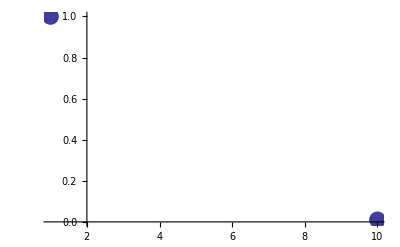

```mathematica
plot12=ListPlot[{{x0,y0},{xf,yf}},PlotStyle->PointSize[0.03]]
```

```mathematica
data12=Table[{X2[i],Y2[i]},{i,0,20}];
data22=Table[{X2[i],Z2[i]},{i,0,20}];
plot22=ListPlot[data1,Joined->True,PlotStyle->{Thickness[0.002],RGBColor[0,1,0]},DisplayFunction->Identity];
plot32=ListPlot[data2,Joined->True,PlotStyle->{Thickness[0.002],RGBColor[1,1,0]},DisplayFunction->Identity];
```

```mathematica
Show[plot12,plot22,plot32,Axes->True,AxesOrigin->{0,0},PlotRange->Automatic]
```

-Graphics-

## Interpolation between 1st and 2nd iteration

Use linear interpolation between first two iterations to generate a better solution

The third assumed dy/dx.

```mathematica
dydx3=(dydx1-dydx2)/(Y1[5]-Y2[5])*(yf-Y2[5])+dydx2
dzdx3=(dzdx1-dzdx2)/(Z1[5]-Z2[5])*(zf-Z2[5])+dzdx2
```

-102.556

-35.4596

```mathematica
X3[0]=x0
Y3[0]=y0
Z3[0]=z0
Q3[0]=dydx3
W3[0]=dzdx3

For[i=0,i<n,i++,
X3[i+1]=X3[i]+h;

k1y=f1[X3[i],Y3[i],Z3[i],Q3[i],W3[i]];
k1z=f2[X3[i],Y3[i],Z3[i],Q3[i],W3[i]];
k1q=f3[X3[i],Y3[i],Z3[i],Q3[i],W3[i]];
k1w=f4[X3[i],Y3[i],Z3[i],Q3[i],W3[i]];

k2y=f1[X3[i]+0.5*h,Y3[i]+0.5*k1y*h,Z3[i]+0.5*k1z*h,Q3[i]+0.5*k1q*h,W3[i]+0.5*k1w*h];
k2z=f2[X3[i]+0.5*h,Y3[i]+0.5*k1y*h,Z3[i]+0.5*k1z*h,Q3[i]+0.5*k1q*h,W3[i]+0.5*k1w*h];
k2q=f3[X3[i]+0.5*h,Y3[i]+0.5*k1y*h,Z3[i]+0.5*k1z*h,Q3[i]+0.5*k1q*h,W3[i]+0.5*k1w*h];
k2w=f4[X3[i]+0.5*h,Y3[i]+0.5*k1y*h,Z3[i]+0.5*k1z*h,Q3[i]+0.5*k1q*h,W3[i]+0.5*k1w*h];

k3y=f1[X3[i]+0.5*h,Y3[i]+0.5*k2y*h,Z3[i]+0.5*k2z*h,Q3[i]+0.5*k2q*h,W3[i]+0.5*k2w*h];
k3z=f2[X3[i]+0.5*h,Y3[i]+0.5*k2y*h,Z3[i]+0.5*k2z*h,Q3[i]+0.5*k2q*h,W3[i]+0.5*k2w*h];
k3q=f3[X3[i]+0.5*h,Y3[i]+0.5*k2y*h,Z3[i]+0.5*k2z*h,Q3[i]+0.5*k2q*h,W3[i]+0.5*k2w*h];
k3w=f4[X3[i]+0.5*h,Y3[i]+0.5*k2y*h,Z3[i]+0.5*k2z*h,Q3[i]+0.5*k2q*h,W3[i]+0.5*k2w*h];

k4y=f1[X3[i]+h,Y3[i]+k3y*h,Z3[i]+k3z*h,Q3[i]+k3q*h,W3[i]+k3w*h];
k4z=f2[X3[i]+h,Y3[i]+k3y*h,Z3[i]+k3z*h,Q3[i]+k3q*h,W3[i]+k3w*h];
k4q=f3[X3[i]+h,Y3[i]+k3y*h,Z3[i]+k3z*h,Q3[i]+k3q*h,W3[i]+k3w*h];
k4w=f4[X3[i]+h,Y3[i]+k3y*h,Z3[i]+k3z*h,Q3[i]+k3q*h,W3[i]+k3w*h];

Y3[i+1]=Y3[i]+1/6*(k1y+2*k2y+2*k3y+k4y)*h;
Z3[i+1]=Z3[i]+1/6*(k1z+2*k2z+2*k3z+k4z)*h;
Q3[i+1]=Q3[i]+1/6*(k1q+2*k2q+2*k3q+k4q)*h;
W3[i+1]=W3[i]+1/6*(k1w+2*k2w+2*k3w+k4w)*h;
]
```

10.

0.01

0.008

-102.556

-35.4596

General::ovfl: Overflow occurred in computation.

```mathematica
plot13=ListPlot[{{x0,y0},{xf,yf}},PlotStyle->PointSize[0.03]]
```

-Graphics-

```mathematica
data13=Table[{X3[i],Y3[i]},{i,0,20}];
data23=Table[{X3[i],Z3[i]},{i,0,20}];
plot23=ListPlot[data1,Joined->True,PlotStyle->{Thickness[0.002],RGBColor[0,1,0]},DisplayFunction->Identity];
plot33=ListPlot[data2,Joined->True,PlotStyle->{Thickness[0.002],RGBColor[1,1,0]},DisplayFunction->Identity];
Show[plot13,plot23,plot33,Axes->True,AxesOrigin->{0,0},PlotRange->Automatic]
```

-Graphics-